### Functions

```mathematica
RuleBlock::usage="RuleBlock[{x_1 → y_1, x_2 → y_2, …}, body] or RuleBlock[<|x_1 → y_1, x_2 → y_2, …|>, body] localizes all the variables x assigning value y_i to x_i then evaluates body. Values are assigned in the order they are provided, therefore it is possible to define dependent values like {a → 2, b → 1/a}. Make sure that none of the x_i has a global value assigned to it.";
SetAttributes[RuleBlock,HoldAll];
RuleBlock[a_,body_]:=Keys@a/.{x__}:>Block[{x},Set@@@Normal@a;body];

ExpandRule[rules_]:=Module[{vars,vals},
{vars,vals}=(List@@@MapAt[If[ListQ@#,#,List@#]&,Normal@rules,{All,-1}])ᵀ;
Outer[(Head@rules)@@Thread[vars->{##}]&,Sequence@@vals,1]
];

SortNatural[list_List]:=Module[{tmp},
tmp=StringSplit[ToString/@list,x:NumberString:>ToExpression@x];
list[[Ordering@PadRight@tmp]]
]

(* NOTE: Do not bother with the error messages if system cannot find a suitable compiler. The following functions work the same if not compiled properly, just that they might not be that fast. *)
binaryVectorHD=Compile[{{a,_Integer,1},{b,_Integer,1}},Total@Abs[a-b],Parallelization->True ,CompilationTarget->"C",RuntimeAttributes->Listable,RuntimeOptions->"Speed"];
binaryVectorAntiHD=Compile[{{a,_Integer,1},{b,_Integer,1}},Length@a-Total@Abs[a-b],Parallelization->True ,CompilationTarget->"C",RuntimeAttributes->Listable,RuntimeOptions->"Speed"];
binaryVectorFitness=Compile[{{a,_Integer,1},{b,_Integer,1}},1.-Total@Abs[a-b]/Length@a,Parallelization->True ,CompilationTarget->"C",RuntimeAttributes->Listable,RuntimeOptions->"Speed"];
binaryVectorMutate=Compile[{{a,_Integer,1},{μ,_Real}},If[RandomReal[]<μ,Abs[#-1],#]&/@a,Parallelization->True ,CompilationTarget->"C",RuntimeAttributes->Listable,RuntimeOptions->"Speed"];
binaryVectorPC=Compile[{{u,_Integer,1},{v,_Integer,1}},Module[{du=u-Mean@N@u,dv=v-Mean@N@v},
Total[du*dv]/(Sqrt@Total[du^2]*Sqrt@Total[dv^2])]];
binaryVectorAntiPC=Compile[{{u,_Integer,1},{v,_Integer,1}},Module[{du=u-Mean@N@u,dv=v-Mean@N@v},
1.0-Total[du*dv]/(Sqrt@Total[du^2]*Sqrt@Total[dv^2])]];
```

### Code

```mathematica
(* Simulating different attractor networks: *)
(*   Realistic attractor network: input triggers the stored pattern that is closest to it. Returned output is then noised. *)
(*   Correlated noisy channel: input is unchanged and only when outputted will it be noised. *)

(*SeedRandom@1;*)
ClearAll[time,n,an,pn,sn,tn,recall,select,retrain,reenter,μO,μL,μR,fitness,closeness];
par=<|
time->3500,(* number of generations *)
n->200, (* pattern length *)
an->20, (* number of attractor networks *)
pn->30, (* number of patterns stored per network *)
sn->1, (* number of selected output patterns (output population size); 1 corresponds to elitist selection *)
tn->{1,2,5,10}, (* training number: each output is trained to this many networks *)
recall->"ClosestStored"(*"ClosestStored"*),(* AAN behaviour: "ClosestStored" returns learned pattern that is closest to input; "RandomStored" returns random stored pattern; "Input" returns input unchanged;  *)
select->"Best", (* method to select among output *)
retrain->"RandomSample",(* method to select networks and stored patterns to rewrite: "RandomSample" or "Random" *)
reenter->"Exhaustive",(* method to generate input: "ShuffledReplaceWorst", "ShuffledReplaceRandom", "Exhaustive" *)
μO->1/200., (* per-bit noise of AAN when returning selected output (O); .005 *)
μT->.01,(* per-bit noise of input when training (T); .01 *)
μI->1/200., (* per-bit noise when reentering input (I); .005 *)
fitness->binaryVectorFitness, (* fitness function to maximize (binaryVectorPC, binaryVectorFitness) *)
closeness->binaryVectorAntiHD (* closeness function to minimize (binaryVectorPC, binaryVectorAntiHD) *)
|>;

model[ass_Association]:=Block[{opt,out,in,net,sel,recallF,selectF,retrainF,reenterF},RuleBlock[ass,
opt=RandomInteger[{0,1},{n}];
in=RandomInteger[{0,1},{an,sn,n}];
net=RandomInteger[{0,1},{an,pn,n}];
recallF=Switch[recall,(* #1: network; #2: input pattern *)
"Random",RandomInteger[{0,1},{n}],
"RandomStored",RandomChoice@#1&,
"ClosestStored",First@MaximalBy[#1,Function[{x},closeness[x,#2]]]&,
"Input",#2&];
selectF=Switch[select,(* #1: output population; *)
"Best",MaximalBy[#,fitness[#,opt]&,sn]&,
"Worst",MinimalBy[#,fitness[#,opt]&,sn]&,
"Random",RandomSample[#,sn]&];
retrainF=Switch[retrain,(* #1: network population; #2: selected outputs *)
"Random",ReplacePart[#1,Flatten[
Thread[{RandomChoice[Range@an,tn],RandomChoice[Range@pn,tn]}ᵀ->Table[binaryVectorMutate[#,μT],{i,tn}]]&/@#2
,1]]&,
"RandomSample",ReplacePart[#1,Flatten[
Thread[{RandomSample[Range@an,tn],RandomSample[Range@pn,tn]}ᵀ->Table[binaryVectorMutate[#,μT],{i,tn}]]&/@#2
,1]]&,(* for each output pattern, generate a random sample of the size `tn`; If there are multiple patterns to learn, later ones can overwrite earlier entries. *)
None,#1&];
reenterF=Switch[reenter,(* generate input; #1: selected outputs; #2: output population; #3: fitness of output population *)
"ShuffledReplaceWorst",Function[{s,o,w},(List/@RandomSample@ReplacePart[o,Take[Flatten[Position[w,#]&/@TakeSmallest[w,sn]],sn]->o])],
"ShuffledReplaceRandom",(List/@RandomSample@ReplacePart[#2,Thread[RandomSample[Range@an,sn]->#1]])&,
"Exhaustive",Table[#1,{an}]&(* use same selected patterns for each network exhaustively *)
];
Transpose@Table[Block[{w},
(* The selected output population is reentered as input in an exhaustive way, *)
(* each network recieves each selected pattern producing an output pattern in turn *)
(* generating thus a new population of `an × sn` patterns *)
(* which is selected and `sn` patterns are chosen for the next generation. *)
out=Flatten[Table[recallF[net[[i]],#]&/@in[[i]],{i,an}],1]; (* returns a joint list of patterns for all inputs and networks *)
out=binaryVectorMutate[#,μO]&/@out;
w=fitness[#,opt]&/@out;
sel=selectF@out;
net=retrainF[net,sel];
in=reenterF[sel,out,w];(* returns a list of patterns for each network *)
in=Map[binaryVectorMutate[#,μI]&,in,{2}];
{Min@w,Max@w,Mean@w}
],{t,time}]
]];

Monitor[
(*AbsoluteTiming@*)(*RuntimeTools`Profile@*)(data=AssociationMap[model,Flatten@ExpandRule@par];),
Dynamic@{an,tn,t}
]
```

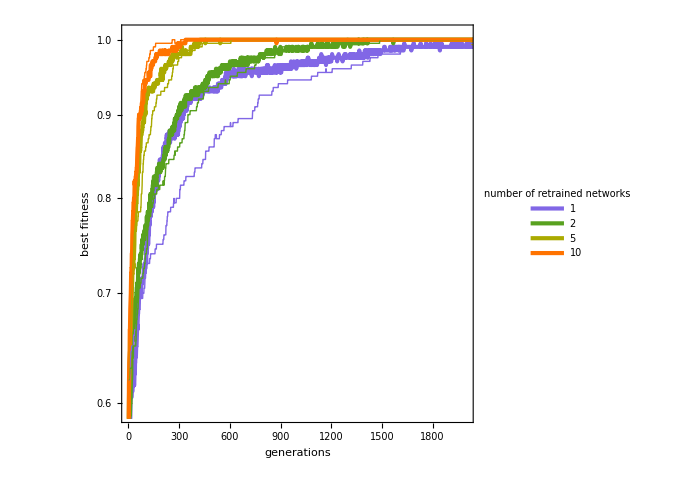

```mathematica
Keys@data;
var=tn;
labels={tn->"number of \nretrained networks",recall->"attractor behaviour"};
label=var/.labels;
y=Max;
name="meta";
colors={Hue[0.7000000000000001, 0.55, 0.9],Hue[0.26, 0.81, 0.63],RGBColor[Rational[2, 3], Rational[2, 3], 0],RGBColor[1, 0.45, 0]};

col=y/.{Min->1,Max->2,Mean->3};
opts={PlotTheme->"Scientific",Background->White,Joined->True,PlotRange->{{0,2000},{.59,1.01}},PlotRangePadding->{Scaled@.01,Scaled@.01},LabelStyle->Directive[Black,16],ImageSize->500,FrameLabel->{"generations","best fitness"},AspectRatio->1,FrameTicks->All,
GridLines->{{},{(*0,1*)}},GridLinesStyle->Directive[GrayLevel@.7,Thick,Dashed],Axes->False,FrameStyle->Directive[Black,AbsoluteThickness@1],PlotLegends->Placed[LineLegend[Thread@Directive[AbsoluteThickness@3,colors],{1,2,5,10},LegendLabel->label],{.8,.4}]};


dir=NotebookDirectory[];
files=Take[SortNatural@FileNames["*.dat",dir],4];
loaded=Table[If[StringMatchQ[#,"#"~~__],Nothing,ToExpression@Part[StringSplit@#,2]]&/@Import[i,"Lines"],{i,files}];
loaded=(PadRight[#,Max[Length/@loaded],Last@#]&/@loaded);
load=ListLogPlot[loaded,PlotStyle->(Directive[AbsoluteThickness@1,(*Darker@*)#]&/@colors),opts];

plot=ListLogPlot[data[[All,col]],PlotStyle->(Directive[AbsoluteThickness@3,(*Darker@*)#]&/@colors),PlotLegends->None,opts];
Show[plot,load]
```